```mathematica
minkowski=Plot[{x/3,3x},{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->{{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed},{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed}},Ticks->None,PlotRangeClipping->False,AxesLabel->{x,t},Epilog->{GrayLevel[0.4],Text[Style[OverBar[x]],{3.4,1.15}],Text[Style[OverBar[t]],{1.15,3.4}]},ImageSize->Small]
```

-Graphics-

```mathematica
γ=1/Sqrt[1-(1/3)^2]
```

3/(2 √2)

```mathematica
α=ArcTanh[1/3]
```

ArcTanh[1/3]

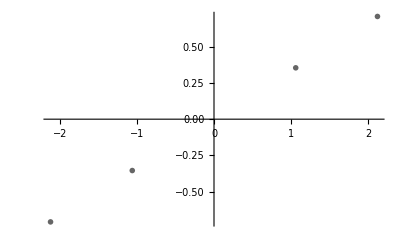

```mathematica
ticksx=ListPlot[{{γ,γ/3},{2γ,2γ/3},{-γ,-γ/3},{-2γ,-2γ/3}},PlotMarkers->{Rotate["-",Pi/2+α]},PlotStyle->{GrayLevel[0.4],PointSize->Small}]
```

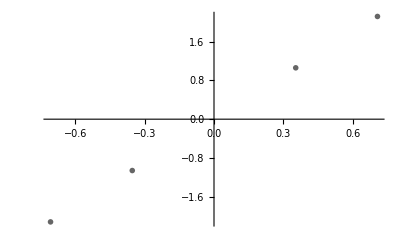

```mathematica
tickst=ListPlot[{{γ/3,γ},{2γ/3,2γ},{-γ/3,-γ},{-2γ/3,-2γ}},PlotMarkers->{Rotate["-",-α]},PlotStyle->{GrayLevel[0.4],PointSize->Small}]
```

```mathematica
mTicks=Plot[{x/3,3x},{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,Ticks->{{-3,-2,-1,1,2,3},{-3,-2,-1,1,2,3}},PlotStyle->{{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed},{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed}},PlotRangeClipping->False,AxesLabel->{x,t},Epilog->{GrayLevel[0.4],Text[Style[OverBar[x]],{3.4,1.15}],Text[Style[OverBar[t]],{1.15,3.4}]},ImageSize->Small]
```

-Graphics-

```mathematica
minkowskiTicks=Show[mTicks,ticksx,tickst]
```

-Graphics-

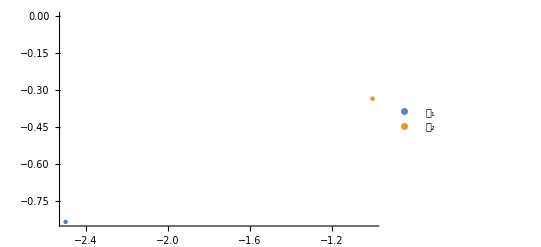

```mathematica
P4a=ListPlot[{{{-2.5,-2.5/3}},{{-1,-1/3}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

```mathematica
lines4a={Graphics[{Thin,Dotted,Line[{{-1,-1/3},{0,-1/3}}]}],Graphics[{Thin,Dotted,Line[{{-2.5,-2.5/3},{0,-2.5/3}}]}]}
```

{-Graphics-,-Graphics-}

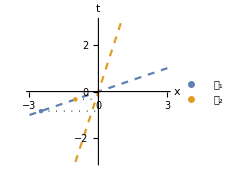

```mathematica
Show[minkowski,lines4a,P4a]
```

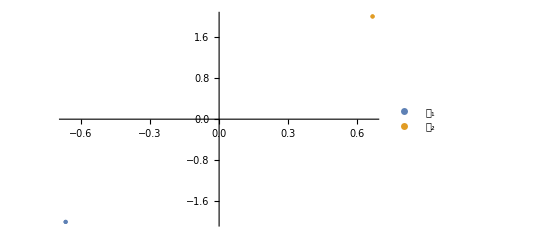

```mathematica
P4b=ListPlot[{{{-2/3,-2}},{{2/3,2}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

```mathematica
lines4b={Graphics[{Thin,Dotted,Line[{{-2/3,-2},{-2/3,0}}]}],Graphics[{Thin,Dotted,Line[{{2/3,2},{2/3,0}}]}]}
```

{-Graphics-,-Graphics-}

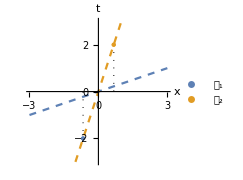

```mathematica
Show[minkowski,lines4b,P4b]
```

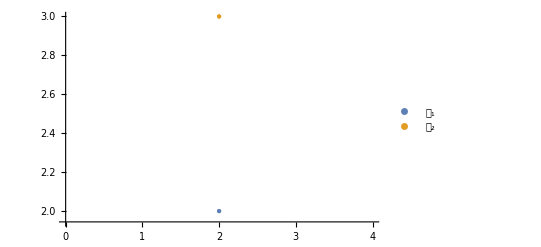

```mathematica
P4c=ListPlot[{{{2,2}},{{2,3}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

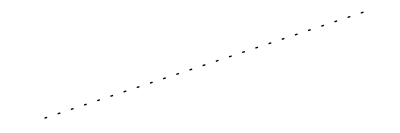
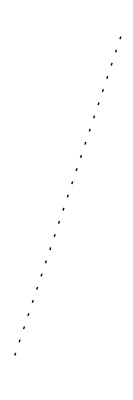
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lines4c={Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2,3},{1/2,5/2}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2,3},{1,0}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2,2},{1/2,3/2}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2,2},{3/2,1/2}}]}],Graphics[{White,Polygon[{{0.63,2},{1.03,3.2},{1/4,3}}]}],
Graphics[{White,Polygon[{{0.95,0.01},{0.95,0.3},{3/2,0.45},{2,0.01}}]}]}
```

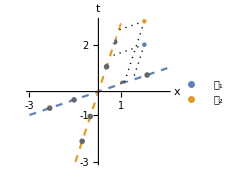

```mathematica
Show[minkowskiTicks,lines4c,P4c]
```

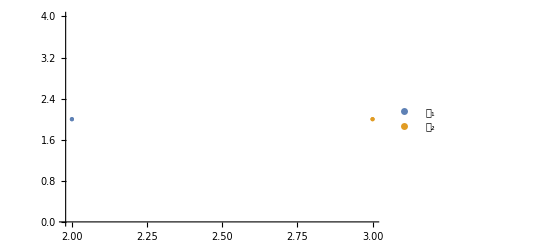

```mathematica
P4d=ListPlot[{{{2,2}},{{3,2}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

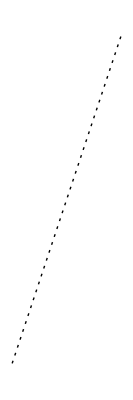
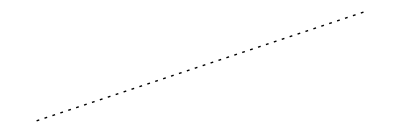
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lines4d={Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{3,2},{5/2,1/2}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{3,2},{0,1}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2,2},{3/2,1/2}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2,2},{1/2,3/2}}]}],Graphics[{White,Polygon[{{2,0.63},{3.2,1.03},{3,1/4}}]}],Graphics[{White,Polygon[{{0.01,0.95},{0.3,0.95},{0.45,3/2},{0.01,2}}]}]}
```

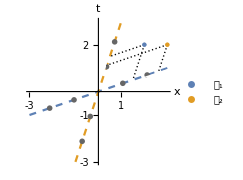

```mathematica
Show[minkowskiTicks,lines4d,P4d]
```

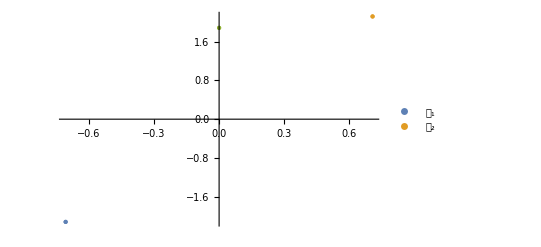

```mathematica
P4e=ListPlot[{{{-2γ/3,-2γ}},{{2γ/3,2γ}},{{0,2/γ}}},PlotStyle->{PointSize[Large]},PlotLegends->{Subscript[𝒫, 1],Subscript[𝒫, 2]}]
```

```mathematica
lines4e={Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{-2γ/3,-2γ},{0,-2γ}}]}],Graphics[{Thin,Dashing[{0.005,0.01}],Line[{{2γ/3,2γ},{0,2γ}}]}]}
```

{-Graphics-,-Graphics-}

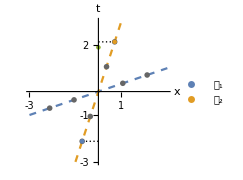

```mathematica
Show[minkowskiTicks,lines4e,P4e]
```

```mathematica
γ
```

3/(2 √2)

```mathematica
N[(4*3)/(2 √2)]
```

4.24264

```mathematica
/2
```